1. Perform 20 iteration of the Newton’ s method to find the smallest positive root of the equation f (x) = Exp[- x]-x;

```mathematica
x0=1;
Nmax=20;
ϵ=0.00000005;
f[x_]:=Exp[-x]-x;
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The error is ",Abs[x0-a]];x0=a];
Print[i," Iteration : ",a]];
Plot[f[x],{x,-1,3}]
```

The error is 0.462117

1 Iteration : 0.537883

The error is 0.0291041

2 Iteration : 0.566987

The error is 0.000156295

3 Iteration : 0.567143

Return[0.567143]

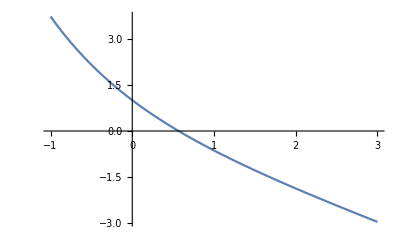

2. Perform 20 iteration of the Newton' s method to find the smallest positive root of the equation f (x) = Cos[x] - x;

The estimated error is 0.249636

1 Iteration the approxmation root : 0.750364

The estimated error is 0.011251

2 Iteration the approxmation root : 0.739113

The estimated error is 0.0000277575

3 Iteration the approxmation root : 0.739085

Return[0.739085]

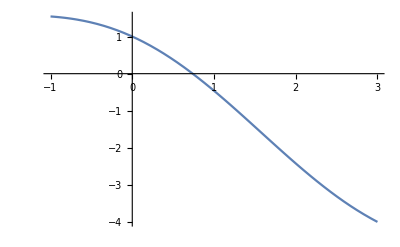

```mathematica
x0=1;
Nmax=20;
ϵ=0.00000005;
f[x_]:=Cos[x]-x;
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The estimated error is ",Abs[x0-a]];x0=a];
Print[i," Iteration the approxmation root : ",x0]];
Plot[f[x],{x,-1,3}]
```

3. Perform 20 iteration of the Newton’s method to find the smallest positive root of the equation f(x) =x^3 + 2 x^2-3x-1 ;

The estimated error is 0.25

1 Iteration the approxmation root : 1.25

The estimated error is 0.0490654

2 Iteration the approxmation root : 1.20093

The estimated error is 0.00223874

3 Iteration the approxmation root : 1.1987

The estimated error is 4.59753×10^-6

4 Iteration the approxmation root : 1.19869

Return[1.19869]

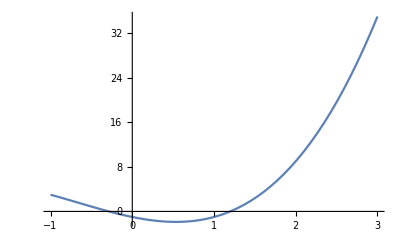

```mathematica
x0=1;
Nmax=20;
ϵ=0.00000005;
f[x_]:= x^3+ 2 x^2-3x-1;
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The estimated error is ",Abs[x0-a]];x0=a];
Print[i," Iteration the approxmation root : ",x0]];
Plot[f[x],{x,-1,3}]
```

4. Perform 20 iteration of the Newton’s method to find the smallest positive root of the equation f(x) =Log[1+x]-Cos[x] ;

The estimated error is 0.113938

1 Iteration the approxmation root : 0.886062

The estimated error is 0.0015508

2 Iteration the approxmation root : 0.884511

The estimated error is 3.24163×10^-7

3 Iteration the approxmation root : 0.884511

Return[0.884511]

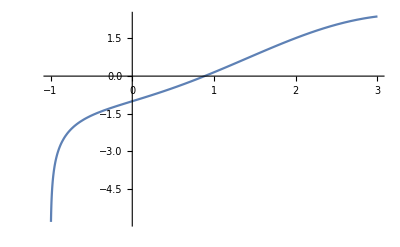

```mathematica
x0=1;
Nmax=20;
ϵ=0.00000005;
f[x_]:= Log[1+x]-Cos[x];
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The estimated error is ",Abs[x0-a]];x0=a];
Print[i," Iteration the approxmation root : ",x0]];
Plot[f[x],{x,-1,3}]
```

5. Perform 20 iteration of the Newton’s method to find the smallest positive root of the equation f(x) =Sin[x]-Cos[x] ;

The estimated error is 0.217958

1 Iteration the approxmation root : 0.782042

The estimated error is 0.00335627

2 Iteration the approxmation root : 0.785398

Return[0.785398]

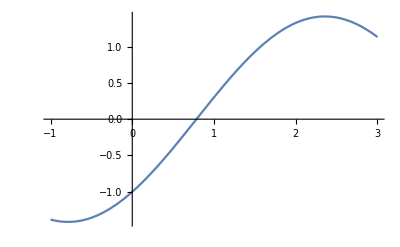

```mathematica
x0=1;
Nmax=20;
ϵ=0.00000005;
f[x_]:= Sin[x]-Cos[x];
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The estimated error is ",Abs[x0-a]];x0=a];
Print[i," Iteration the approxmation root : ",x0]];
Plot[f[x],{x,-1,3}]
```

6. Perform 20 iteration of the Newton’s method to find the smallest positive root of the equation f(x) =x^3-3x-5 ;

The estimated error is 0.333333

1 Iteration the approxmation root : 2.33333

The estimated error is 0.0527778

2 Iteration the approxmation root : 2.28056

The estimated error is 0.00153549

3 Iteration the approxmation root : 2.27902

The estimated error is 1.28178×10^-6

4 Iteration the approxmation root : 2.27902

Return[2.27902]

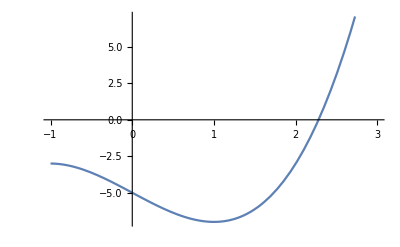

```mathematica
x0=2;
Nmax=20;
ϵ=0.00000005;
f[x_]:= x^3-3x-5;
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The estimated error is ",Abs[x0-a]];x0=a];
Print[i," Iteration the approxmation root : ",x0]];
Plot[f[x],{x,-1,3}]
```

The error is 0.00704225

1 Iteration : 2.49296

The error is 0.0000210604

2 Iteration : 2.49294

Return[2.49294]

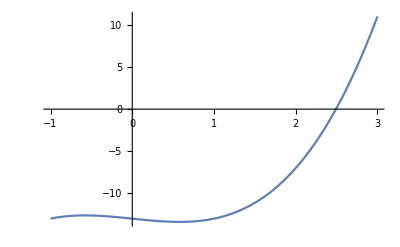

```mathematica
x0=2.5;
Nmax=20;
ϵ=0.00000005;
f[x_]:=x^3-x-13;
For[i=1,i≤Nmax,i++,a=N[x0-(f[x0]/f'[x0])];
If[Abs[x0-a]<ϵ,Return[x0],Print[" The error is ",Abs[x0-a]];x0=a];
Print[i," Iteration : ",a]];
Plot[f[x],{x,-1,3}]
```